```mathematica
agu=FullSimplify[SeriesCoefficient[1/Log[y+3/4 x^2],{x,2/(√3)√(1-y),-1}]/SeriesCoefficient[1/Log[y+3/4 x^2],{x,2/(√3)√(1-y),0}]]
```

(4 (-1+y))/(√(3-3 y) (-1+2 y))

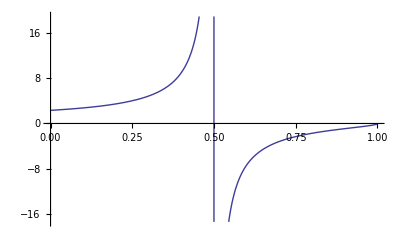

```mathematica
Plot[agu,{y,0,1}]
```

```mathematica
Series[1/Log[y+3/4 x^2],{x,2/(√3)√(1-y),1}]
```

1/(√3 √(1-y) (x-(2 √(1-y))/(√3)))+(-1+2 y)/(4 (-1+y))+((√3-8 √3 y+4 √3 y^2) (x-(2 √(1-y))/(√3)))/(48 √(1-y) (-1+y))+O[x-(2 √(1-y))/(√3)]^2

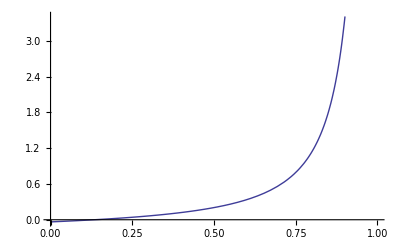

```mathematica
Plot[((1-8 y+4 y^2)/(16 √3 √(1-y) (-1+y))),{y,0,1}]
```

```mathematica
SeriesCoefficient[1/Log[y+3/4 x^2],{x,2/(√3)√(1-y),1}]
```

(1-8 y+4 y^2)/(16 √3 √(1-y) (-1+y))